# Detrended Fluctuation Analysis

Borrador

```mathematica
IIDx[size_]:=Block[{𝒫,data,x},
𝒫=WhiteNoiseProcess[];
data=RandomFunction[𝒫,{size}];
x = Normal[data][[1]];
Return[x];
];
CreateX[x_]:=Block[{μ,X},
μ = Mean[x[[All,2]]];
X = Table[{x[[t,1]],Sum[x[[i,2]]-μ,{i,1,t}]},{t,1,Length[x]}];
Return[X];
];
CreateY[X_,n_]:=Partition[X,n];
CreateYn[Y_]:=Block[{fits, a, b,n,ynparam,x,k},
fits = Table[CoefficientList[Fit[Y[[j]], {1,x},x],x],{j,1,Length[Y]}];
a = fits[[All,2]];
b = fits[[All,1]];
n = Length[Y[[1]]];
ynparam=Table[{a[[i]]k + b[[i]],(i-1)*n≤ k<i*n},{i, 1,Length[Y]}];
Return[ynparam];
];
F[x_,n_]:=Block[{Xv,Yv,yn,Nn,Y},
Xv = CreateX[x];
Yv = CreateY[Xv,n];
yn[k_]:= Piecewise[CreateYn[Yv]];
Nn = Length[Xv];
Y = Interpolation[Xv,InterpolationOrder->1];
Return[√(1/Nn Sum[(Y[k]-yn[k])^2,{k,0,Nn-1}])];
];
DFAPlot[x_,nmin_,nmax_]:=Block[{model,fit,fnVsN,α,c,n},
fnVsN = Table[{n,F[x,n]},{n,nmin,nmax}];
model = c n^α;
fit = FindFit[fnVsN,model,{c,α},n];
Plot[model /.fit,{n,nmin,nmax},Epilog->{PointSize[Medium],Point[fnVsN]},PlotTheme->"Scientific",FrameLabel->{"n","F(n)"}]
];
DFA[x_,nmin_,nmax_]:=Block[{model,fit,fnVsN,α,c,n},
fnVsN = Table[{n,F[x,n]},{n,nmin,nmax}];
model = c n^α;
fit = FindFit[fnVsN,model,{c,α},n];
Return[α /.fit];
];
```

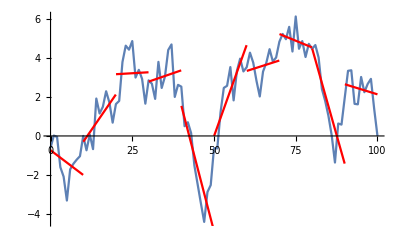

```mathematica
xv = IIDx[100];
Xv = CreateX[xv];
Yv = CreateY[Xv,10];

yn[k_]:= Piecewise[CreateYn[Yv]];
Show[
ListLinePlot[Xv],
Plot[yn[k],{k,0,100},PlotStyle->Red]
]
```

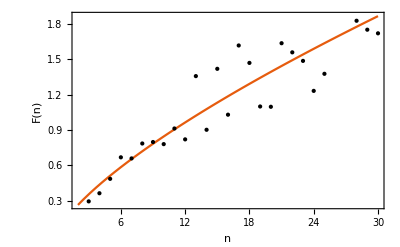

```mathematica
DFAPlot[IIDx[100],2,30]
```

```mathematica
DFA[IIDx[100],2,30]
```

0.621409